-Graphics-

C:\C_files\HW5\report\Q1(1).png

-Graphics-

C:\C_files\HW5\report\Q1(2).png

1.11613

0.968566

-Graphics-

C:\C_files\HW5\report\Q2(1).png

-Graphics-

C:\C_files\HW5\report\Q2(2).png

1.1436

-Graphics-

C:\C_files\HW5\report\Q3(1).png

-Graphics-

C:\C_files\HW5\report\Q3(2).png

0.959049

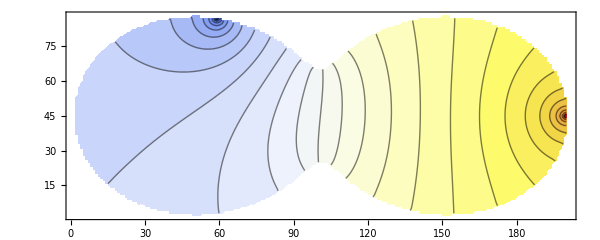

C:\C_files\HW5\report\Q4(1).png

-Graphics-

C:\C_files\HW5\report\Q4(2).png

```mathematica
(*Q1*)
a=Import["C:\\C_files\\HW5\\q1_NX=300.txt","Table"];
picQ2=ListContourPlot[a,ImageSize->600,AspectRatio->2/3,PlotRange->Full,PlotLegends->Automatic,Contours->30,ColorFunction->"TemperatureMap"]
Export["C:\\C_files\\HW5\\report\\Q1(1).png",picQ2]
b=Import["C:\\C_files\\HW5\\q1_NX=300_inverse.txt","Table"];
picQ2=ListContourPlot[b,ImageSize->600,AspectRatio->2/3,PlotRange->Full,PlotLegends->Automatic,Contours->30,ColorFunction->"TemperatureMap"]
Export["C:\\C_files\\HW5\\report\\Q1(2).png",picQ2]
R1=0.248355+0.242514;
R2=0.017833-(-0.014927);
E^(-π R1)+E^(-π R2)
(*Q2*)
R1=0.293313+0.293313;
R2=-(-0.033495)+ 0.033495;
E^(-π R1)+E^(-π R2)
a=Import["C:\\C_files\\HW5\\q2_H=0.01.txt","Table"];
picQ2=ListContourPlot[a,ImageSize->600,AspectRatio->2/3,PlotRange->Full,PlotLegends->Automatic,Contours->25,ColorFunction->"TemperatureMap"]
Export["C:\\C_files\\HW5\\report\\Q2(1).png",picQ2]
b=Import["C:\\C_files\\HW5\\q2_H=0.01_inverse.txt","Table"];
picQ2=ListContourPlot[b,ImageSize->600,AspectRatio->2/3,PlotRange->Full,PlotLegends->Automatic,Contours->30,ColorFunction->"TemperatureMap"]
Export["C:\\C_files\\HW5\\report\\Q2(2).png",picQ2]
(*Q3*)
R1=0.129034-(-0.048891);
R2=0.129034-(-0.048891);
E^(-π R1)+E^(-π R2)
a=Import["C:\\C_files\\HW5\\q3_H=0.01.txt","Table"];
picQ2=ListContourPlot[a,ImageSize->600,AspectRatio->2/3,PlotRange->Full,PlotLegends->Automatic,Contours->25,ColorFunction->"TemperatureMap"]
Export["C:\\C_files\\HW5\\report\\Q3(1).png",picQ2]
b=Import["C:\\C_files\\HW5\\q3_H=0.01_inverse.txt","Table"];
picQ2=ListContourPlot[b,ImageSize->600,AspectRatio->2/3,PlotRange->Full,PlotLegends->Automatic,Contours->30,ColorFunction->"TemperatureMap"]
Export["C:\\C_files\\HW5\\report\\Q3(2).png",picQ2]
(*Q4*)
R1=-1.656232+2.985171;
R2=-0.197188+0.215642;
E^(-π R1)+E^(-π R2)
a=Import["C:\\C_files\\HW5\\q4.txt","Table"];
picQ2=Show[ListContourPlot[a,ImageSize->600,AspectRatio->2/5,PlotRange->Full,PlotLegends->Automatic,Contours->30,ColorFunction->"TemperatureMap"]]
Export["C:\\C_files\\HW5\\report\\Q4(1).png",picQ2]
b=Import["C:\\C_files\\HW5\\q4_inverse.txt","Table"];
picQ2=Show[ListContourPlot[b,ImageSize->600,AspectRatio->2/5,PlotRange->Full,PlotLegends->Automatic,Contours->30,ColorFunction->"TemperatureMap"]]
Export["C:\\C_files\\HW5\\report\\Q4(2).png",picQ2]
```